```mathematica
Clear["Global`*"]
```

```mathematica
A=0.9; B=0.65;
```

```mathematica
DE={x'[t]==A+x[t]^2 y[t] - (B+1) x[t],
y'[t]==B x[t] - x[t]^2 y[t],
x[0]==0.5,
y[0]==0.8}
```

{x'[t]==0.9-1.65 x[t]+x[t]^2 y[t],y'[t]==0.65 x[t]-x[t]^2 y[t],x[0]==0.5,y[0]==0.8}

```mathematica
sols=NDSolve[DE,{x,y},{t,0,30}]
```

{{x→InterpolatingFunction[{{0., 30.}}, <>],y→InterpolatingFunction[{{0., 30.}}, <>]}}

```mathematica
fx[t_]=First[x[t]/.sols]
```

InterpolatingFunction[{{0., 30.}}, <>][t]

```mathematica
fy[t_]=First[y[t]/.sols]
```

InterpolatingFunction[{{0., 30.}}, <>][t]

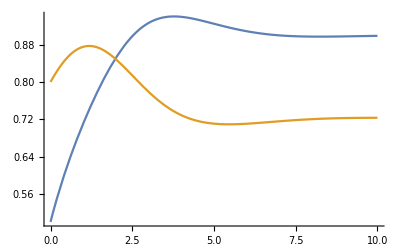

```mathematica
Plot[{fx[t],fy[t]}, {t,0,10}]
```

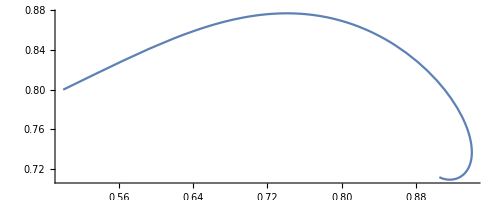

```mathematica
ParametricPlot[{fx[t],fy[t]}, {t, 0, 2*Pi}]
```